# Lista II - Mecânica Estatística

Lyliana Myllena Santos de Sousa - 11223740
Lyliana.sousa@usp.br

## 1.a)

Supondo que a energia dos sistemas sempre se conservam, então temos que: 
●	Para o sistema isolado, que possui uma partícula vermelha com 6 unidades de energia, essa partícula pode ocupar apenas o nível com 6 unidades de energia, portanto, só possui 1 microestado acessível, o com 6 unidades de energia.
●	Para o sistema B, temos duas partículas ( branca e azul) que não interagem, portanto não podem ocupar o mesmo nível de energia, e as duas partículas juntas possuem uma energia total de 2 unidades. Assim, nesse sistema só temos dois microestados acessíveis, os estados (2,0) e (0,2).
Vimos também no Rosser, que existe uma expressão que nos diz a quantidade de microestados acessíveis um sistema pode ter sobre uma determinada energia, sendo essa expressão:
Ω_B(U_B) = [N_B +U_B - 1]/((N_B-1)!U_B!) (1.1), sendo U_Ba energia do sistema B, N_Bo número de partículas do sistema B.
No entanto no nosso caso, essa expressão precisa ser ligeiramente alterada, já que nossas partículas não podem coabitarem o mesmo nível de energia, portanto, subtrairmos um microestado quando nossa energia é par, para excluir o microestado onde as partículas coexistem.

## 1.b)

Agora com os nossos sistemas unidos por uma parede adiatérmica, ou seja, em  contato térmico. A energia total do nosso sistema composto será de 8 unidades de energia. Utilizando a expressão (1.1) , criarei uma tabela indicando a quantidade de microestados para cada configuração de energia:

-Graphics-

Observando a tabela acima temos que o numero total de microestados no nosso sistema serão dados a partir de uma relação de energia U_Total = U_A +U_B=8 ⟶ U_B = 8 - U_A:
Ω_Total(U_A,U_B)= ∑_U_A Ω_A(U_A)Ω_B(U_B)= ∑_U_A Ω_A(U_A)Ω_B( 8 - U_A)= 40 microestados acessíveis.

## 1.c)

O equilíbrio térmico ocorrerá quando U_A= U_B=4 , primeiro vou calcular a entropia inicial do sistema, que ocorre quando o sistema tem U_A = 6  e U_B = 2. Neste, equilíbrio temos que a sua entropia é:
S_inicial = K_b ln(Ω_A(U_A)Ω_B( 8 - U_A))  K_b ln(Ω_A(6)Ω_B( 2))= K_b ln(2).
A entropia final, que ocorre quando as energias para ambos os sistemas são iguais, temos que a sua entropia é:
S_final = K_b ln(Ω_A(U_A)Ω_B( 8 - U_A)) = K_b ln(Ω_A(4)Ω_B( 4)= K_b ln(4).
Com isso, tenho que a ariação da entropia é:
ΔS = K_b(ln(4) - ln(2)) =K_b ln(2)= 9.56993×10^-24  (m^2 Kg)/(s^2 K)

```mathematica
1.38064852*10^-23*Log[2]
```

9.56993×10^-24

## 1.d)

Para calcular  o valor médio da energia de cada sistema no equilíbrio, utilizarei a expressão:
OverBar[U_A] = (∑_U_A U_A Ω_A(U_A)Ω_B( 8 - U_A))/(Ω_Total(U_A,U_B)) = 100/40=5/2=2,5
OverBar[U_B] = (∑_U_A (8 - U_A)Ω_A(U_A)Ω_B( 8 - U_A))/(Ω_Total(U_A,U_B)) = 220/40=11/2=5,5
Podemos ver que esses resultados estão certos, pela conservação de energia, a soma das energias dever sempre resultar em 8 unidades de energia.

## 2.

Nosso sistema composto possui as seguintes relações: N=N_A+N_B=8, E_Total=E_A+E_B=20, N_A=3 E N_B=5 . Sendo Pr(E_B) a probabilidade de que o sistema B contenha E_B unidades de energia, Ω_A (E_A) o número de microestados acessíveis ao sistema A quando ele contém E_A unidades de energia e por Ω_B (E_B) o número de microestados acessíveis ao sistema B quando ele contém E_B unidades de energia. Como todo os nossos gráficos serão descritos em termos de E_B, usarei a relação N_A=8 - N_B  e E_A=20 - E_B.
Para todos os gráficos que farei, tenho que E_B terá uma escala de [0, 20] , portanto não faz tanta diferença os níveis de energia infinitos, pois as partículas não conseguiram acessar níveis de energia com energia maior que 20 unidades de energia.
Número de microestados acessíveis para o valor de E_B.
Ω_A(E_A) = Ω_A (20 - E_B) =((N_A + E_A -1)!)/((N_A-1)!E_A !)  = ((22 -  E_B )!)/((2)!(20 - E_B)!) 
Ω_B(E_B) =((N_B + E_B -1)!)/((N_B-1)!E_B !)  = ((4 + E_B )!)/((4)!( E_B)!) 
Número total de microestados para todos os valores possíveis de E_B.
Ω_TB = ∑_(E_B=0)^20 ((4 + E_B )!)/((4)!( E_B)!)((22 -  E_B )!)/((2)!(20 - E_B)!) = 888030 microestados acessíveis.
Probabilidade que o sistema B contenha E_B energias.
Pr(E_B) = (Ω_B(E_B)Ω_A(20 - E_B))/Ω_TB= 1/888030*((4 + E_B )!)/((4)!( E_B)!)*((22 -  E_B )!)/((2)!(20 - E_B)!)
A partir dessas relações eu consigo plotar  gráficos de Pr(E_B) , de ln Ω_B (E_B), de ln Ω_A (20 − E_B),
de ln[ Ω_A (20 − E_B)Ω_B(E_B)] e de lnPr(E_B) , todos em função de  E_B.

```mathematica
omegaTB = ∑_(Subscript[E, B]=0)^20 ((4 + Subscript[E, B] )!)/((4)!( Subscript[E, B])!)((22 -  Subscript[E, B] )!)/((2)!(20 - Subscript[E, B])!)
```

888030

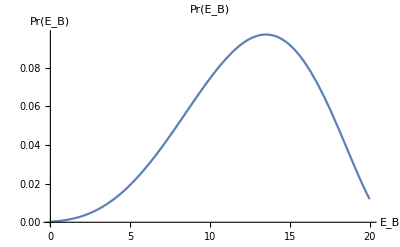

```mathematica
(*Plotando  Pr(Subscript[E, B]) em função de Subscript[E, B]*)
Plot[ 1/888030*((4 + x )!)/((4)!( x)!)*((22 -  x )!)/((2)!(20 - x)!),{x,0,20}, AxesLabel-> {"E_B",Pr("E_B")}, PlotLabel->"Pr(E_B)"]
```

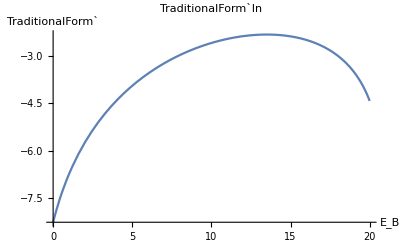

```mathematica
(*Plotando  ln(Pr(Subscript[E, B])) em função de Subscript[E, B]*)
Plot[Log[ 1/888030*((4 + x )!)/((4)!( x)!)*((22 -  x )!)/((2)!(20 - x)!)],{x,0,20}, AxesLabel-> {"E_B","TraditionalForm`"}, PlotLabel->"TraditionalForm`ln"]
```

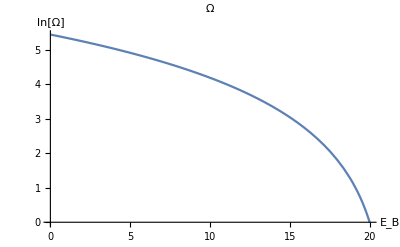

```mathematica
(*Plotando  ln[Subscript[Ω, A](20 − Subscript[E, B])] em função de Subscript[E, B]*)
Plot[ Log[((22 -  x )!)/((2)!(20 - x)!)],{x,0,20}, AxesLabel-> {"E_B","ln[Ω]"}, PlotLabel->"Ω"]
```

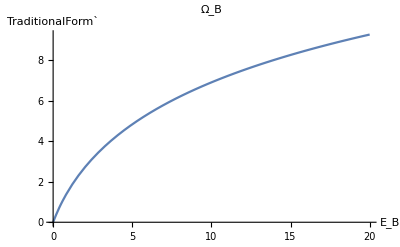

```mathematica
(*Plotando  ln[Subscript[Ω, B](Subscript[E, B])] em função de Subscript[E, B]*)
Plot[ Log[((4 + x )!)/((4)!( x)!)],{x,0,20}, AxesLabel-> {"E_B","TraditionalForm`"}, PlotLabel->"Ω_B"]
```

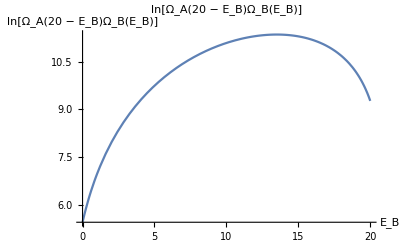

```mathematica
(*Plotando  ln[Subscript[Ω, A](20 − Subscript[E, B])Subscript[Ω, B](Subscript[E, B])] em função de Subscript[E, B]*)
Plot[ Log[((4 + x )!)/((4)!( x)!)((22 -  x )!)/((2)!(20 - x)!)],{x,0,20}, AxesLabel-> {"E_B","ln[Ω_A(20 − E_B)Ω_B(E_B)]"}, PlotLabel->"ln[Ω_A(20 − E_B)Ω_B(E_B)]"]
```

## 3.a)

Existe uma expressão que descreve a flutuação relativa, para isso tenho que, sendo: r_A=V_A/V, r_B=V_(B/V), ρ = N/V, temos que  flutuação relativa da metade de A é:
σ/N_A^* = (√(r_A r_B ρ(1 - ρ)V))/(ρ r_A V)
Do enunciado do exercício temos que V = V_A + V_B = 10^12, porém a caixa está dividida ao meio portanto, V_A=V_B=1/2 V. Assim, r_A =r_B = (1/2).
σ/N_A^* = (√(r_A r_B ρ(1 - ρ)V))/(ρ r_A V)= (√((1/4)(N/V)(1 - N/V)V))/((N/V)(1/2)V) = (√((N/V)(V - N)))/N = √((V - N)/NV) = √(1/N-1/V)
Assim, para a flutuação relativa de 1% na metade de A, tenho o seguinte número de partículas em A. POrtanto, tenho que:
0.01 = √(1/N - 1/V) =  √(1/N - 10^-12)⟶ 10^4 - 10^-12 = 1/N ⟶ N ≈ 10000 moléculas

## 3.b)

Partindo da fórmula acima, tenho que o número de moléculas será dado por:
σ/N_A^* = √(1/N-1/V) ⟶ 10^-6 = √(1/N - 10^-12) ⟶ N = 1/2*10^12 moléculas

## 3.c)

A probabilidade para que em um microestado tenha N_A partículas na metade de A é:
P(N_A)ΔN = (Ω_B(N_B)Ω_A(N_A))/(∑_N_A Ω_B(N_B)Ω_A(N_A)) = 1/(V
N) (v_A!)/(N_A! (v_A -N_A)!)  (V_B!)/((V_B - N_B)!N_B!) = (N! (V -N)!)/(V!) (v_A!)/(N_A! (v_A -N_A)!)  (V_B!)/((V_B - N_B)!N_B!) 
Para todas as partículas em A tenho que : N_A=N e N_B=0. Com isso tenho que a seguinte expressão para a probabilidade.
P(N_A)ΔN  =  ((1/2 V)!(V -N)!)/(V! (1/2 V -N)!)  
●	Probabilidade do item a, onde o número de moléculas é 10^4 pode ser expressa por:
P(N_A)ΔN  =  ((1/2 10^12)!(10^12 -10^4)!)/(10^12! (1/2 10^12 -10^4)!)  
●	Probabilidade do item B, onde o número de moléculas é 1/2*10^12pode ser expressa por:
P(N_A)ΔN  =  ((1/2 10^12)!(10^12 -1/2*10^12)!)/(10^12! (1/2 10^12 -1/2*10^12)!)  =([(1/2 10^12)!]^2)/(10^12!)  
Note, que eu deixei a probabilidade sem um valor numérico, isso foi porque o mathematica não tinha memoria suficiente para calcular esse valor.

```mathematica
((Factorial[0.5*10^12])^2)/Factorial[10^12]
```

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

Throw::sysexc: Uncaught SystemException returned to top level. Can be caught with Catch[…, _SystemException].

SystemException[MemoryAllocationFailure]

## 4.

O sistema A e B, que são separados por uma parede rígida, impermeável e adiabática, são regidos pela mesma equação fundamental: S^(A)=(R^2/(v_0 θ))^(1/3) (N_A V_A U_A)^(1/3) e S^(B)=(R^2/(v_0 θ))^(1/3) (N_B V_B U_B)^(1/3) , onde os seus parâmetros são dados por: R, v_0,θ>0, N_A=18,06*10^23 moléculas, N_B= 12,04*10^23 moléculas, V_A= 9*10^-6 m^3e V_B= 4*10^-6 m^3, U= U_A+ U_B= 80J. Para os gráficos da entropia  como função de U_A/(U_A+U_B), tenho as seguintes expressões:
S^(A)=(R^2/(v_0 θ))^(1/3) (N_A V_A U_A/(U_A+ U_B))^(1/3)=(R^2/(v_0 θ))^(1/3) (N_A V_A U_A/80)^(1/3) e  S^(B)=(R^2/(v_0 θ))^(1/3) (N_B V_B(80 - U_A)/(U_A+ U_B))^(1/3)= (R^2/(v_0 θ))^(1/3) (N_B V_B(80 - U_A)/80)^(1/3)

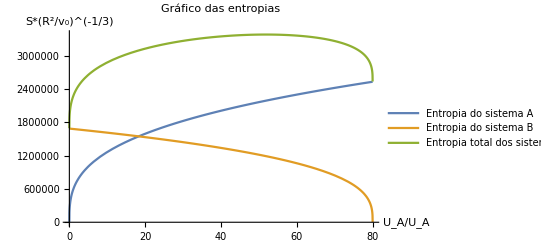

```mathematica
sa[x_]:= (18.06*10^23*9*10^-6 x/80)^(1/3)
sb[x_]:= (12.04*10^23*4*10^-6(80-x)/80)^(1/3)
st[x_]:= sa[x] + sb[x]
Plot[{sa[x],sb[x],st[x]},{x,0,80}, AxesLabel-> {"U_A/U_A","S*(R^2/v_0)^(-1/3)"}, PlotLabel->"Gráfico das entropias", PlotLegends->{"Entropia do sistema A","Entropia do sistema B","Entropia total dos sistemas"}]
```

Quando mudamos a parede por uma adiatérmica, após um tempo o nosso sistema atinge o equilíbrio térmico, que, ou seja, a temperatura no sistema A é a mesma do sistema B. Após equilíbrio térmico as energias internas e temperaturas do sistema se alteram. No entanto, pela conservação de energia, a soma das energias finais permanecem 80J. Com isso, temos as seguintes relações de temperatura:
1/T_A=((∂S^(A))/(∂U_A)) = (R^2/(v_0 θ))^(1/3) (N_A V_A)^(1/3) 1/(3(U_(A-final))^(2/3)) ⟶ 1/T_B=((∂S^(B))/(∂U_B)) = (R^2/(v_0 θ))^(1/3) (N_B V_B)^(1/3) 1/(3(U_(B-final))^(2/3))  ⟷ (N_A V_A)^(1/3)/(3(U_(A-final))^(2/3)) = (N_B V_B)^(1/3)/(3(U_(B-final))^(2/3))⟷(U_(A-final))/(U_(B-final)) = √((N_A V_A)/(N_B V_B)) ⟷U_(A-final) = 3(√6)/4 U_(B-final)
U_(A-final)+U_(B-final) =80 J
Das relações acima, eu tenho que as novas energias internas são dadas por: U_(A-final) = 51,8 J e U_(B-final)=28,2 J

## 5.a)

Nesse exercício, temos um sistema composto por dois cilindros conectados por uma membrana semi-permeável, a qual apenas as partículas do cilindro 1 podem transitar, mantendo assim, sempre o mesmo numero de partículas no cilindro dois.
Esses sistemas possuem as seguintes característica inicialmente:
Sistema 1:  N_1^(1) = 0,5 mol, N_2^(1) = 0,75 mol, V_1=5 litros, T_1^(1)=300K
Sistema 2: N_1^(2) = 1 mol, N_2^(2) = 0,5 mol, V_2=5 litros, T_1^(2)=250K
Lembrando que como o nosso sistema  é um sistema fechado, sua energia e número de partículas são conservadas, ou seja: V = V_1 + V_2 = 10 litros, N^(1) = N_1^(1) + N_1^(2) e U = U_1+U_2.
Onde ambos são regidos pela equação de estado:
S^(1) = N^(1)A + N^(1)R ln((U_1^(3/2)V_1)/((N^(1))^(5/2))) - N_1^(1)R ln(N_1^(1)/N^(1)) -  N_2^(1)R ln(N_2^(1)/N^(1))  , para o sistema 1
S^(2) = N^(2)A + N^(2)R ln((U_2^(3/2)V_2)/((N^(2))^(5/2))) - N_1^(2)R ln(N_1^(2)/N^(2)) -  N_2^(2)R ln(N_2^(2)/N^(2))  , para o sistema 2
Para obter a função de temperatura do nosso sistema, fazemos:
1/T^(1)=((∂S^(1))/(∂U_1))_(V_1,N^(1))= 3/2 R/U_1 N^(1)= 3/2 R/U_1[ N_1^(1) + N_2^(1)] (5.1)		 1/T^(2)=((∂S^(2))/(∂U_2))_(V_2,N^(2))= 3/2 R/U_2 N^(2)= 3/2 R/U_2[ N_1^(2) + N_2^(2)] (5.2)
Para obter a função do potencial químico do nosso sistema, fazemos:
µ_2/T^(2) =((∂S^(2))/(∂N^(2)))_(V_2,U_2)=A +Rln((U_2^(3/2)V_2)/((N^(2))^(5/2))) - 5/2 R - Rln(N_1^(2)/N^(2))		µ_1/T^(1) =((∂S^(1))/(∂N^(1)))_(V_1,U_1)=A +Rln((U_1^(3/2)V_1)/((N^(1))^(5/2))) - 5/2 R - Rln(N_1^(1)/N^(1))
 As condições de equilíbrio para o nosso sistema serão: 1/T^(1)= 1/T^(2) e µ_1/T^(1)=µ_2/T^(2)
Disso, nos teremos dois sistemas, onde lembrando que devido as características da nossa membrana, temos que apenas  N_1^(1) e  N_1^(2) se alteram, portanto:

Piecewise[{{3/2 R/U_1[ N_1^(1) + N_2^(1)]=3/2 R/U_2[ N_1^(2) + N_2^(2)], }, {A +Rln((U_2^(3/2)V_2)/((N_1^(2) + N_2^(2))^(5/2))) - 5/2 R - Rln(N_1^(2)/(N_1^(2) + N_2^(2)))=A +Rln((U_1^(3/2)V_1)/(( N_1^(1) + N_2^(1))^(5/2))) - 5/2 R - Rln(N_1^(1)/(N_1^(1) + N_2^(1))), }}]
Piecewise[{{1/U_1[ N_1^(1) + 0.75]=1/U_2[ N_1^(2) + 0.5], }, {(1/N_1^(2)[U_2/(N_1^(2) + 0.5)])^(5/2) =(1/N_1^(1)[U_1/(N_1^(1) + 0.75)])^(5/2), }}] ⟶ 1/N_1^(2) =1/N_1^(1) ⟶  N_1^(1) = N_1^(2)
Assim, eu tenho que N^(1) = N_1^(1) + N_1^(2)= 2 N_1^(1) = 1.5 ⟶ N_1^(1) = N_1^(2) = 0.75 partículas

## 5.b)

Para conseguir obter o valor de T no equilíbrio, primeiro vou calcular o valor das energias internas do nosso cilindro inicialmente. Para isso usarei as expressões (5.1) e (5.2),
1/T^(1)= 3/2 R/U_1 [N_1^(1) + N_2^(1)] ⟶ U_(1-inicial)= (3R T^(1)(N_1^(1) + N_2^(1)))/2 = 4668,75 J
1/T^(2)= 3/2 R/U_2 [N_1^(2) + N_2^(2)] ⟶ U_(2-inicial)= (3R T^(2)(N_1^(2) + N_2^(2)))/2 = 4668,75 J
Agora, vou calcular o valor das energias no equilíbrio, sabendo que as energias se conservam portanto  (U_(1-inicial))_+ U_(2-inicial) =(U_(1-final))_+ U_(2-final) = 9337,5 J . No item a, encontramos a relação: U_1 = (N_1^(1) + N_2^(1))/(N_1^(2) + N_2^(2)) U_2 = 6/5 U_2, substituindo essa relação na equação de conservação da energia interna temos as energias finais:  U_(1-final)= 5093,18 J e U_(2-final)=4244,3 . Assim, sabendo o valor das energias no equilíbrio temos que a temperatura temos que:
1/T= 3/2(R N^(1))/U_1= 3/2(R N^(2))/U_2⟶ T= (2 U_1)/(3 R N^(1))= (2 U_2)/(3 R N^(2)) = 272.72 K

## 5.c)

Para obter o valor da pressão no equilíbrio utilizo a expressão: p = T ((∂S)/(∂V))_(N,U)= T NR/V. Assim, as pressões serão dadas por:
p_1 = T RN^(1)/V_1 = (272,72*8,3*1,5)/5 = 679,1 Pa 
p_2 = T RN^(2)/V_2 = (272,72*8,3*1,25)/5 =565,9 Pa

## 6.a)

A equação fundamental de energia por quantidade de partículas, para sólidos cristalinos é dada por: u(v,s)= Ae^((b(v - v_0))^2)s^(4/3)e^(s/3 K_b), para A,B,v_0,K_B>0. Temos a seguinte relação para a temperatura:
T= ((∂u)/(∂s))_(v,n)= 4/3 s^(1/3)Ae^((b(v - v_0))^2)e^(s/3 K_b)+A/(3 K_b)e^((b(v - v_0))^2)s^(4/3)e^(s/3 K_b).
Para T = 0, temos a seguinte relação de entropia:
0= 4/3 s^(1/3)Ae^((b(v - v_0))^2)e^(s/3 K_b)+A/(3 K_b)e^((b(v - v_0))^2)s^(4/3)e^(s/3 K_b)=Ae^((b(v - v_0))^2)e^(s/3 K_b)( 4/3 s^(1/3)+s^(4/3)/(3 K_b)) ⟶s^(1/3)( 4+s/K_b)=0  , portanto, como não podemos ter entropia  negativa, temos que para T = 0, temos S = 0.

## 6.b)

Pelo item A, temos que T = A/3 e^((b(v - v_0))^2)e^(s/3 K_b)( 4 s^(1/3)+s^(4/3)/K_b), portanto para baixas temperaturas temos baixas entropias, assim, para valores pequenos de s, tenho que s^(4/3)≈0 e e^(s/3 K_b)≈1. Com essas aproximações temos a seguinte relação para a temperatura. T = (4A)/3 e^((b(v - v_0))^2)e^(s/3 K_b) s^(1/3). Com isso, tenho a seguinte relação para a entropia,  s=(27T.b3)/((4 Ae^((b(v - v_0))^2)e^(s/3 K_b))^3)= αT^3 . 
A expressão para o calor específico é obtida fazendo: c_v = T((∂S)/(∂T)) = 3 αT^3, portanto, o calor especifico é proporcional a temperatura a terceira, para temperaturas baixas.

## 6.c)

Ainda usando a expressão que eu obtive no item A, tenho que para temperaturas muito grandes teremos entropias muito grandes, com isso tenho a seguinte aproximação da equação da temperatura para temperaturas muito altas:
ln(T) = s/(3 K_B) + ln( A/3 e^((b(v - v_0))^2)( 4 s^(1/3)+s^(4/3)/K_b)), para isso tenho que s/(3 K_B) ≫ ln( A/3 e^((b(v - v_0))^2)( 4 s^(1/3)+s^(4/3)/K_b)). Portanto a entropia para temperaturas muito altas pode ser dada por s= 3 K_b ln(T). Com isso, tenho a seguinte relação do calor especifico para temperaturas muito altas: c_v = T ((∂S)/(∂T)) =T 3 K_b 1/T=3 K_b